```mathematica
T1[e13_,e23_]:=Catch[Module[{colc={e13,e23},mem={0,0}},
mem[[1]]=If[colc[[1]]≤1&&colc[[1]]≥0,colc[[1]],1/colc[[1]]];
mem[[2]]=If[colc[[2]]≤1&&colc[[2]]≥0,colc[[2]],1/colc[[2]]];
mem[[1]]=Mod[mem[[2]],mem[[1]]];
Throw[mem[[1]]];
]]
Px[x_]:=x-1/2 Floor[1/2 (-1+Sqrt[-7+8 x])] (1+Floor[1/2 (-1+Sqrt[-7+8 x])]);Py[x_]:=1/2 (2-2 x+Ceiling[1/2 (-1+Sqrt[1+8 x])]+Ceiling[1/2 (-1+Sqrt[1+8 x])]^2);
```

```mathematica
Test[xx_,yy_,zz_,zz2_]:=Catch[Module[{colc={xx,yy,zz,zz2},mem},
If[colc[[4]]-colc[[2]]==0,Throw[0];];
mem=Floor[Mod[1/T1[colc[[1]],colc[[3]]],colc[[4]]-colc[[2]]]];
Throw[mem];
]];
FactInt[zzr_,zzr2_]:=Catch[Module[{colc=zzr,colc2=zzr2,mem={0,2,0,0,0,0,0,0},mem2,mem3={0,0,0},dat={},dat2={},dat3={},cnt={0,0,1},swt=0},
If[colc<5000,Throw[FactorInteger[colc]]];
mem2=Floor[Log[colc]^2];
mem[[3]]=Floor[(mem2 mem2/Floor[Log[mem2]]^2)/ⅇ];
mem[[8]]=2 mem[[3]];
mem[[5]]=Floor[ⅇ mem2];
mem3[[2]]=Floor[√colc];
mem3[[1]]=Floor[√mem3[[2]]];
dat=Table[Prime[the1],{the1,1,Floor[Log[mem[[3]]]]}];
mem[[7]]=Length[dat];

Label["GoGo"];
If[cnt[[1]]>mem2,Throw[{"Failed"}];];
mem[[1]]=Test[colc,mem[[5]]+cnt[[1]],mem3[[1]],mem3[[2]]];
If[mem[[1]]<colc2[[1]],cnt[[1]]++;Goto["GoGo"];];
If[mem[[1]]>colc2[[2]],cnt[[1]]++;Goto["GoGo"];];
mem[[6]]=mem[[1]]-mem[[3]];
cnt[[2]]=0;
cnt[[3]]=1;
dat2=Table[Mod[mem[[6]],dat[[yyet]]],{yyet,1,mem[[7]]}];
If[MemberQ[dat2,0]==True,cnt[[2]]++;];

Label["GoGo1aa"];
swt=0;
cnt[[3]]=1;
If[cnt[[2]]≥mem[[8]],cnt[[1]]++;Goto["GoGo"];];

Label["GoGo1a"];
If[cnt[[3]]>mem[[7]],cnt[[3]]=1;swt=0;Goto["GoGo1b"]];
If[Mod[cnt[[2]]+dat2[[cnt[[3]]]],dat[[cnt[[3]]]]]==0,cnt[[3]]=1;swt=1;Goto["GoGo1b"];];
cnt[[3]]++;Goto["GoGo1a"];

Label["GoGo1b"];
If[swt==1,cnt[[2]]++;cnt[[3]]=1;Goto["GoGo1aa"];,Goto["GoGo2"];];

Label["GoGo2"];
mem[[4]]=Abs[mem[[6]]+cnt[[2]]];
If[mem[[4]]==1||mem[[4]]==0,cnt[[2]]++;Goto["GoGo1aa"];];
mem[[4]]=Mod[colc,mem[[4]]];
If[mem[[4]]==0,Goto["GoGo3"];];
swt=0;cnt[[2]]++;Goto["GoGo1aa"];

Label["GoGo3"];
Throw[Abs[mem[[6]]+cnt[[2]]]];
]];
```

```mathematica
$MaxExtraPrecision=10000;
```

```mathematica
memr=Prime[80000]Prime[70000];
```

```mathematica
{Timing[FactInt[memr,{Floor[√(√memr)],Floor[√memr]}]],Timing[FactorInteger[memr]]}
```

{{100.35,882377},{0.004791,{{882377,1},{1020379,1}}}}

```mathematica
Mod[2+5+4,7]
```

4

```mathematica
Prime[300000]
```

4256233

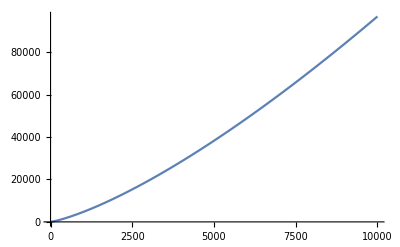

```mathematica
Plot[Pn[bn],{bn,1,10000}]
```

```mathematica
Timing[FactInt[Prime[2000]Prime[3000],{8000,40000}]]
```

{13.6015,17389}

```mathematica
Floor[1375/60]
```

```mathematica
50
```

```mathematica
5500 mins
```

5500 mins

```mathematica
Row[{1,IntegerDigits[Prime[3100000]Prime[2000000],2],22,IntegerDigits[Prime[31000000]Prime[20000000],2]}]
```

1{1,0,1,1,1,1,1,0,1,1,1,1,0,0,1,0,1,0,1,0,1,1,1,0,1,1,1,0,1,0,1,0,1,1,1,0,1,0,1,1,1,0,1,0,1,1,0,0,0,0,1}22{1,1,0,0,0,1,0,0,1,1,1,0,1,0,0,1,0,1,0,1,1,0,1,0,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,0,0,1,0,0,1,0,1,0,1,1,0,0,0,1,0,0,0,1}

```mathematica
Prime[20000000]
```

373587883

```mathematica
Test[mem,7]-Floor[Log[2,mem]]
```

1226

```mathematica
N[Log[2,Prime[20]Prime[300]]]
```

17.1061

```mathematica
{FactorInteger[915],Prime[20]}
```

{{{3,1},{5,1},{61,1}},71}